# Wolfram Language Basics: Week 1 Review

## Friday, Feb 19 2021

## Requests for Review

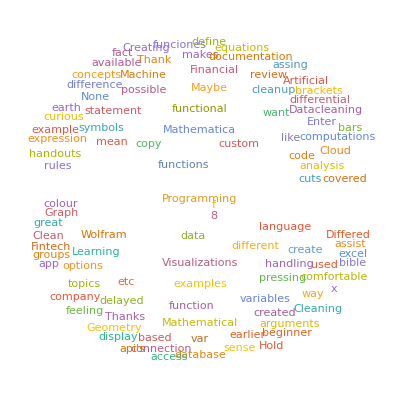

## Shift Enter to Evaluate

```mathematica
2+4
```

6

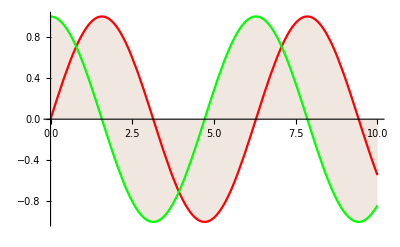

```mathematica
Plot[{Sin[x], Cos[x]},{x,0,10},PlotStyle->{Red,Green},Filling->Axis,FillingStyle->LightBrown]
```

You can use enter to spread out your code over multiple lines for better readability:

```mathematica
Plot[
{Sin[x], Cos[x]},
{x,0,10},
PlotStyle->{Red,Green},
Filling->Axis,
FillingStyle->LightBrown
]
```

-Graphics-

## Natural Language Input



```mathematica
Plot[Sin[x], {x, 0, 2*Pi}]
```

WolframAlphaQueryParseResults

TimeSeries[…]

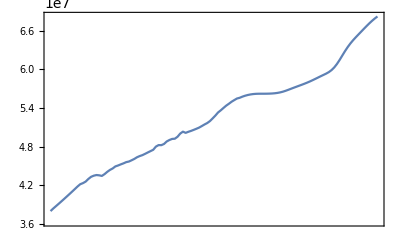

```mathematica
DateListPlot[%]
```

## Four Kinds of Brackets

Four kinds of brackets are used in the Wolfram Language, each serving a different purpose.

### Parentheses for grouping operations

```mathematica
a+b/c
```

```mathematica
(a+b)/c
```

### Square brackets for functions

```mathematica
RandomInteger[]
```

0

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Plot[Sin[x],{x,0, 2 Pi}]
```

-Graphics-

If I have a defined a function:

```mathematica
myFunction[x_,y_]:= x^2 +3 y
```

When I use this function later, I will use square brackets to provide the arguments x and y:

```mathematica
myFunction[2,3]
```

13

### Curly braces for lists

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
RandomColor[10]
```

{RGBColor[0.15144107434373977, 0.5742234611616877, 0.8428492999431785],RGBColor[0.03482159306619881, 0.5239749205193416, 0.2742612733952947],RGBColor[0.2505561843040691, 0.4875206642186036, 0.11291173275844546],RGBColor[0.5592362352182614, 0.3816864850496353, 0.33838849727578535],RGBColor[0.4469479499083848, 0.6135104407459016, 0.6346575318607126],RGBColor[0.9455599617457493, 0.2558757429373273, 0.3218651625116764],RGBColor[0.9789665910168872, 0.6659295768507809, 0.42379914232864],RGBColor[0.10419417330711744, 0.8671608970780145, 0.9205805825052529],RGBColor[0.2615223181637867, 0.6896313819202942, 0.6616654691349484],RGBColor[0.09082691749604122, 0.27715863727692636, 0.7685726835466684]}

### Double brackets for indexing

```mathematica
data ={{4,RGBColor[0.03510323394848891, 0.012308050845976304, 0.30222271161955194],"rheumatoid"},{3,RGBColor[0.5510194486330771, 0.2214333511496751, 0.00728933307344759],"environment"},{0,RGBColor[0.6869896512337175, 0.7464102565473456, 0.04880836489301754],"drawn"},{3,RGBColor[0.06831806273437713, 0.9138301265407274, 0.5927525549181671],"garnish"},{10,RGBColor[0.0696273350329022, 0.7063331758462725, 0.38081194595182444],"flip"},{6,RGBColor[0.7919588762428051, 0.42338788930294924, 0.876725084190517],"scraps"},{6,RGBColor[0.98162365467542, 0.7492727063527906, 0.643822563736421],"estranged"},{2,RGBColor[0.1313933372663414, 0.22613785293138888, 0.990443147677361],"darkness"},{9,RGBColor[0.09602432793787452, 0.21014249303789234, 0.13802612738489461],"disorganize"},{10,RGBColor[0.7752118344649594, 0.082087900386417, 0.26360664691225],"spate"}}
```

{{4,RGBColor[0.03510323394848891, 0.012308050845976304, 0.30222271161955194],rheumatoid},{3,RGBColor[0.5510194486330771, 0.2214333511496751, 0.00728933307344759],environment},{0,RGBColor[0.6869896512337175, 0.7464102565473456, 0.04880836489301754],drawn},{3,RGBColor[0.06831806273437713, 0.9138301265407274, 0.5927525549181671],garnish},{10,RGBColor[0.0696273350329022, 0.7063331758462725, 0.38081194595182444],flip},{6,RGBColor[0.7919588762428051, 0.42338788930294924, 0.876725084190517],scraps},{6,RGBColor[0.98162365467542, 0.7492727063527906, 0.643822563736421],estranged},{2,RGBColor[0.1313933372663414, 0.22613785293138888, 0.990443147677361],darkness},{9,RGBColor[0.09602432793787452, 0.21014249303789234, 0.13802612738489461],disorganize},{10,RGBColor[0.7752118344649594, 0.082087900386417, 0.26360664691225],spate}}

```mathematica
TableForm[data]
```

4 | RGBColor[0.03510323394848891, 0.012308050845976304, 0.30222271161955194] | rheumatoid
3 | RGBColor[0.5510194486330771, 0.2214333511496751, 0.00728933307344759] | environment
0 | RGBColor[0.6869896512337175, 0.7464102565473456, 0.04880836489301754] | drawn
3 | RGBColor[0.06831806273437713, 0.9138301265407274, 0.5927525549181671] | garnish
10 | RGBColor[0.0696273350329022, 0.7063331758462725, 0.38081194595182444] | flip
6 | RGBColor[0.7919588762428051, 0.42338788930294924, 0.876725084190517] | scraps
6 | RGBColor[0.98162365467542, 0.7492727063527906, 0.643822563736421] | estranged
2 | RGBColor[0.1313933372663414, 0.22613785293138888, 0.990443147677361] | darkness
9 | RGBColor[0.09602432793787452, 0.21014249303789234, 0.13802612738489461] | disorganize
10 | RGBColor[0.7752118344649594, 0.082087900386417, 0.26360664691225] | spate

```mathematica
data[[1]]
```

{4,RGBColor[0.03510323394848891, 0.012308050845976304, 0.30222271161955194],rheumatoid}

```mathematica
data[[1,2]]
```

RGBColor[0.03510323394848891, 0.012308050845976304, 0.30222271161955194]

```mathematica
data[[3,2]]
```

RGBColor[0.6869896512337175, 0.7464102565473456, 0.04880836489301754]

## Part Function

```mathematica
TableForm[data]
```

4 | RGBColor[0.03510323394848891, 0.012308050845976304, 0.30222271161955194] | rheumatoid
3 | RGBColor[0.5510194486330771, 0.2214333511496751, 0.00728933307344759] | environment
0 | RGBColor[0.6869896512337175, 0.7464102565473456, 0.04880836489301754] | drawn
3 | RGBColor[0.06831806273437713, 0.9138301265407274, 0.5927525549181671] | garnish
10 | RGBColor[0.0696273350329022, 0.7063331758462725, 0.38081194595182444] | flip
6 | RGBColor[0.7919588762428051, 0.42338788930294924, 0.876725084190517] | scraps
6 | RGBColor[0.98162365467542, 0.7492727063527906, 0.643822563736421] | estranged
2 | RGBColor[0.1313933372663414, 0.22613785293138888, 0.990443147677361] | darkness
9 | RGBColor[0.09602432793787452, 0.21014249303789234, 0.13802612738489461] | disorganize
10 | RGBColor[0.7752118344649594, 0.082087900386417, 0.26360664691225] | spate

First row:

```mathematica
data[[1]]
```

{4,RGBColor[0.03510323394848891, 0.012308050845976304, 0.30222271161955194],rheumatoid}

Last row:

```mathematica
data[[-1]]
```

{10,RGBColor[0.7752118344649594, 0.082087900386417, 0.26360664691225],spate}

First column:

```mathematica
data[[All,1]]
```

{4,3,0,3,10,6,6,2,9,10}

Last column:

```mathematica
data[[All,-1]]
```

{rheumatoid,environment,drawn,garnish,flip,scraps,estranged,darkness,disorganize,spate}

Specific element:

```mathematica
data[[6,3]]
```

scraps

Documentation on Part

Tutorial on “Getting pieces of Lists”

## Shorthand Notations

### Part [[]]

```mathematica
lst = {a,b,c,d,e}
```

{a,b,c,d,e}

```mathematica
Part[lst,3]
```

c

```mathematica
lst[[3]]
```

c

### Postfix and Prefix

```mathematica
ToUpperCase[{"Hello","World"}]
```

{HELLO,WORLD}

```mathematica
ToUpperCase@{"Hello","World"}
```

{HELLO,WORLD}

```mathematica
{"Hello","World"}//ToUpperCase
```

{HELLO,WORLD}

### ReplaceAll /.

```mathematica
ReplaceAll[{1,3,"NA",5,"NA",6,7,8},"NA"-> 0]
```

{1,3,0,5,0,6,7,8}

```mathematica
{1,3,"NA",5,"NA",6,7,8}/."NA"-> 0
```

{1,3,0,5,0,6,7,8}

Documentation on Wolfram Language Syntax: ["http://reference.wolfram.com/language/guide/Syntax.html"](http://reference.wolfram.com/language/guide/Syntax.html)

## Repeated Evaluations

You know how many times to iterate:

```mathematica
Table[(i^2+4)^3,{i,1,10}]
```

{125,512,2197,8000,24389,64000,148877,314432,614125,1124864}

```mathematica
Table[i^2,{i,{1,4,7,10}}]
```

{1,16,49,100}

```mathematica
Nest[fun,x,5]
```

fun[fun[fun[fun[fun[x]]]]]

```mathematica
NestList[fun,x,5]
```

{x,fun[x],fun[fun[x]],fun[fun[fun[x]]],fun[fun[fun[fun[x]]]],fun[fun[fun[fun[fun[x]]]]]}

```mathematica
Fold[fun,x,{1,2,3,4}]
```

fun[fun[fun[fun[x,1],2],3],4]

```mathematica
FoldList[fun,x,{1,2,3,4}]
```

{x,fun[x,1],fun[fun[x,1],2],fun[fun[fun[x,1],2],3],fun[fun[fun[fun[x,1],2],3],4]}

Functional programming approach:

```mathematica
words = TextWords["Wolfram Language Basics: Welcome to Programming"]
```

{Wolfram,Language,Basics,Welcome,to,Programming}

```mathematica
Map[StringLength,words]
```

{7,8,6,7,2,11}

```mathematica
StringLength/@words
```

{7,8,6,7,2,11}

```mathematica
Head[words]
```

List

```mathematica
words//FullForm
```

List["Wolfram","Language","Basics","Welcome","to","Programming"]

```mathematica
Apply[StringJoin,words]
```

WolframLanguageBasicsWelcometoProgramming

```mathematica
Clear[f]
```

```mathematica
Map[f,{a,b,c}]
```

{f[a],f[b],f[c]}

```mathematica
Apply[f,{a,b,c}]
```

f[a,b,c]

## Defining Functions

Input arguments are to be provided as input1_, input2_ and so on...

Use := to define the function

```mathematica
myFunction2[a_,b_] := a + 4 b
```

```mathematica
result = 42;
```

```mathematica
myFunction3[a_,b_] := Module[{result},Echo[result];result=a + 4 b; {result,1/result}]
```

```mathematica
myFunction3[4,5]
```

result$348229

{24,1/24}

## Missed on Day 2: Patterns

```mathematica
NotebookOpen[FileNameJoin[{NotebookDirectory[],"02BeginningProgramming.nb"}]]
```

Slides 26-29

## Procedural vs. Functional vs. Rule-based Programming

Day 2: Slide 30

## Custom Styles

```mathematica
Style["This is special",Green,Bold,42]
```

This is a piece of text. We can format the text using the “Format” menu.

Custom styles can be defined using stylesheets. Here is a tutorial on Working With Stylesheets. (["http://reference.wolfram.com/language/tutorial/WorkingWithStylesheets.html"](http://reference.wolfram.com/language/tutorial/WorkingWithStylesheets.html))

## Wolfram One

Wolfram Cloud

Wolfram Desktop

## Next Week

Advanced Programming: Pure Functions, Non-standard evaluation (Hold, HoldAll)

Working with Data: Data Cleaning, Importing data from XLS

Introduction to Machine Learning

## Resources for Topics We Could not Cover

Differential Equation: Overview (["http://reference.wolfram.com/language/tutorial/DSolveOverview.html"](http://reference.wolfram.com/language/tutorial/DSolveOverview.html))

Statistical Data Visualization: Statistical Visualization (https://reference.wolfram.com/language/guide/StatisticalVisualization.html)

Financial Data Analysis: Financial Computation (["http://reference.wolfram.com/language/guide/Finance.html"](http://reference.wolfram.com/language/guide/Finance.html)), Financial Visualization (["http://reference.wolfram.com/language/guide/FinancialVisualization.html"](http://reference.wolfram.com/language/guide/FinancialVisualization.html))

Tensor operations: Symbolic Tensors guide and Symbolic Tensors tutorial  (["http://reference.wolfram.com/language/guide/SymbolicTensors.html"](http://reference.wolfram.com/language/guide/SymbolicTensors.html), ["http://reference.wolfram.com/language/tutorial/SymbolicTensors.html"](http://reference.wolfram.com/language/tutorial/SymbolicTensors.html))

Using Python with the Wolfram Language:

Configure Python for ExternalEvaluate

External Language Interfaces